# Spring with drift

## Free-space solution starting at x0 > 0, traveling to the left at speed v.

```mathematica
Clear[p]
```

```mathematica
ClearAll
d = 0.5
k = 1
x0 = 5
v= 0.01
σ = 0.1
```

ClearAll

0.5

1

5

0.01

0.1

```mathematica
FP = D[p[x, t], t]  ==D[(x-x0+v*t)*p[x, t], x] + d*D[p[x,t], x, x]
```

p^(0,1)[x,t]==p[x,t]+(-5+0.01 t+x) p^(1,0)[x,t]+0.5 p^(2,0)[x,t]

```mathematica
mol[n_Integer,o_: "Pseudospectral"]:={"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MaxPoints"->n,"MinPoints"->n,"DifferenceOrder"->o}}
```

```mathematica
soln=NDSolve[{FP,
			p[x,0]== Exp[-((x-x0)/σ)^2/2]/(σ*Sqrt[2π]),
			p[0, t]==0,
			p[10, t] == 0
			},
			   p,{x,0, 10},{t, 0, 9000}
			   (*Method->mol[18000, 4]*)]
```

{{p→InterpolatingFunction[{{0., 10.}, {0., 9000.}}, <>]}}

```mathematica
Manipulate[Plot[p[x,t]/.soln, {x, 0, 10}, PlotRange-> {-0.01, 1}], {t, 0, 500}]
```

## Integrate to get survival probability

```mathematica
S[t] = Integrate[p[x,t]/.soln, {x, 0, 12}]
```

InterpolatingFunction::dmvali: The integration endpoint 12 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: -9.10863×10^-308 (-0.0323625) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -9.10863×10^-308 (-0.0161812) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -9.10863×10^-308 0.0323625 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{InterpolatingFunction[…][t]}

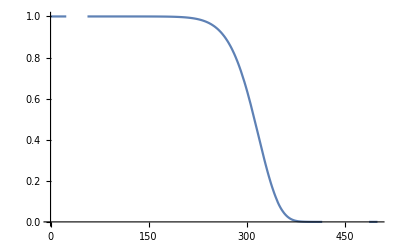

```mathematica
Plot[S[t], {t, 0, 500}, PlotRange->{0, 1}]
```

## Get first-passage time probability

```mathematica
f[t_] =-D[S[t], t]
```

{-InterpolatingFunction[…][t]}

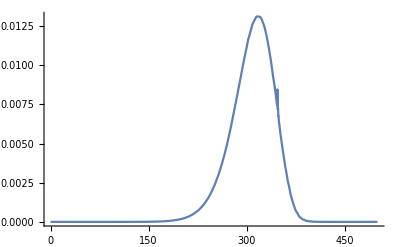

```mathematica
Plot[f[t], {t, 0,500}, PlotRange->All]
```

### Define a function to get the FPT distribution for a set of parameters.

```mathematica
FPT[d_,k_, x0_, v_]:=Module[{mol, σ, tf,xf, FP, soln, S},
σ=0.05*Sqrt[2*d/k];
tf = Ceiling[x0/v];
xf = x0+4*Sqrt[2*d/k];
FP = D[p[x, t], t]  ==D[(x-x0+v*t)*p[x, t], x] + d*D[p[x,t], x, x];
soln=NDSolve[{
			FP,
			p[x,0]== Exp[-((x-x0)/σ)^2/2]/(σ*Sqrt[2π]),
			p[0, t]==0,
			p[xf, t] == 0
		        },
			   p,{x,0, xf},{t, 0, tf}(*,Method-> {"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MaxPoints"->10*tf,"MinPoints"->10*tf,"DifferenceOrder"->4}}*)
			];
S[t] = Integrate[p[x,t]/.soln, {x, 0, xf}] ;
Return[-D[S[t], t]];
]
```

## Plots and scaling

## Behavior with v near crossover

```mathematica
x0Constant = 2
vCrossover = N[x0Constant*Erfc[x0Constant]]
vRange = Reverse[N[PowerRange[5*^-5,2*^-2 , 3]]]
 DConstant = 0.5
 kConstant = 1
```

2

0.00935547

{0.01215,0.00405,0.00135,0.00045,0.00015,0.00005}

0.5

1

```mathematica
results =FPT[DConstant,kConstant, x0Constant, #]&/@vRange
```

General::munfl: -5.07352×10^-307 (-0.0140515) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -5.07352×10^-307 0.0140515 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -5.07352×10^-307 (-0.00702576) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]}}

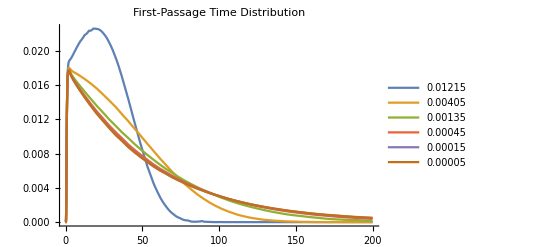

```mathematica
Plot[results, {t, 0, 200}, PlotRange->All, PlotLegends->vRange, PlotLabel->"First-Passage Time Distribution"]
```

## Behavior with x0 near crossover

```mathematica
x0Range = Range[1, 7, 1]
vConstant = 1*^-3
x0Crossover = FindRoot[vConstant - x*(1-Erf[x]), {x, 2}]
 DConstant = 0.5
kConstant = 1
```

{1,2,3,4,5,6,7}

1/1000

{x→2.50348}

0.5

1

```mathematica
results =FPT[DConstant,kConstant, #, vConstant]&/@x0Range
```

General::munfl: 3.29208×10^-306 (-0.00629723) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.93187×10^-308 (-0.00629723) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -4.08071×10^-308 (-0.00629723) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]}}

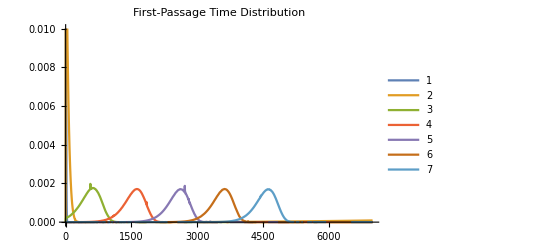

```mathematica
Plot[results, {t, 0, 7000}, PlotLegends->x0Range, PlotLabel->"First-Passage Time Distribution", PlotRange->{0, 0.01}]
```

#### Scaling with D

```mathematica
Clear[x0, d, v, k]
vConstant = 0.01
 DRange = PowerRange[0.1, 45, 2.7]
 kConstant = 1
x0Constant = 15
DCrossover = NSolve[(x0Constant/vConstant )== 1/Erfc[Sqrt[kConstant/(2*d)]*x0Constant], d]
```

0.01

{0.1,0.27,0.729,1.9683,5.31441,14.3489,38.742}

1

15

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{d→19.4301}}

```mathematica
results =FPT[#,kConstant, x0Constant, vConstant]&/@DRange
```

General::munfl: -9.57366×10^-308 (-0.00747168) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -9.57366×10^-308 0.00747168 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -9.57366×10^-308 (-0.00373584) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]}}

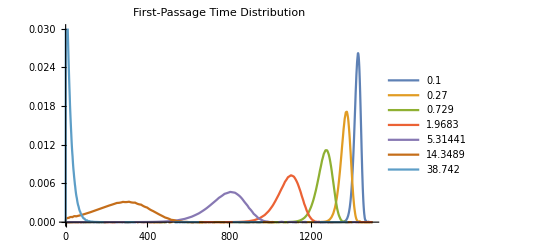

```mathematica
Plot[results, {t, 0, 1500}, PlotLegends->DRange, PlotLabel->"First-Passage Time Distribution", PlotRange->{0, 0.03}]
```